# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - Left Handed Helicity Fraction - SM )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

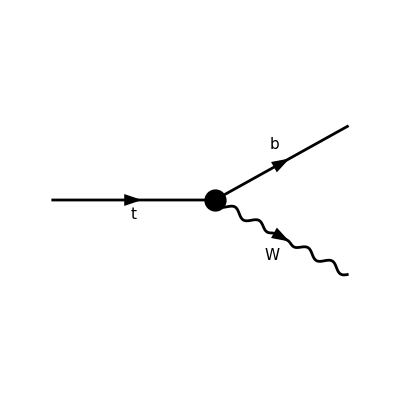

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

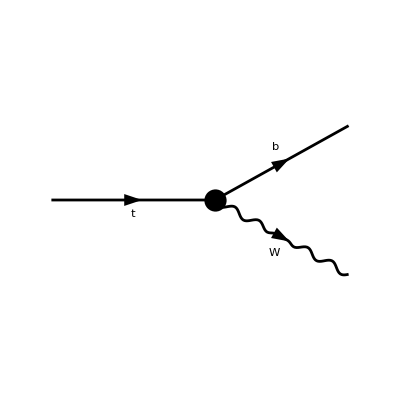

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

1/(32 Lambda^8)Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+8 g Lambda^2 Conjugate[CHud] (g Conjugate[CudH4D] (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^4+√2 mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev+mb Conjugate[CKM3x3] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))))) vev^2+4 mb Conjugate[CKM3x3] (2 g Conjugate[CudH4D] (ⅈ √2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW))+ⅈ ((OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))))+((ε̄)^*(pW)·ε̄(pW)) (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 √2 (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW]) vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev^3+Conjugate[C1qdWH3] (-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-4 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-2 √2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^2+4 Lambda^2 Conjugate[CbW] (-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) ((OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)))-2 ⅈ √2 g (ϵ̄)^(OverBar[pt]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))-√2 g ((OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 (g^2 (Conjugate[CudH4D])^2 (ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))) vev^8+2 √2 g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW))+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-2 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))) vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 (2 ⅈ (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) (OverBar[pt]·OverBar[pW])+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-(OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-ⅈ (((ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW))-ⅈ ((OverBar[pb]·ε̄(pW)) (OverBar[pt]·(ε̄)^*(pW))+(OverBar[pb]·(ε̄)^*(pW)) (OverBar[pt]·ε̄(pW)))) OverBar[pW]^2-(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+(ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)))+((OverBar[pb]·OverBar[pt]) OverBar[pW]^2-2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW])) ((ε̄)^*(pW)·ε̄(pW))))+(Conjugate[CKM3x3])^2 (-16 g^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-64 √2 CtW g mt vev (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^6-128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^4+128 ⅈ CtW^2 vev^2 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-16 ⅈ g^2 vev^4 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 √2 C1quWH3 g mt vev^3 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-64 √2 CtW g mt vev^3 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-256 CtW^2 vev^2 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^4+128 CtW^2 vev^2 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^4-32 g^2 vev^4 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^4-128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW)) Lambda^2+128 ⅈ C1quWH3 CtW vev^4 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW)) Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C3q2H4D CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 √2 C1quWH3 g mt vev^5 Conjugate[C3phiq] (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-256 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Lambda^2+128 C1quWH3 CtW vev^4 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW)) Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2-64 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D) Lambda^2+32 √2 CtW g mt vev^5 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D) Lambda^2-32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW]ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·ε̄(pW)) (OverBar[pW]·(ε̄)^*(pW))+32 ⅈ C1quWH3^2 vev^6 (ϵ̄)^(OverBar[pb]OverBar[pt]OverBar[pW](ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))-32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) (OverBar[pW]·(ε̄)^*(pW)) (OverBar[pW]·ε̄(pW))+4 C2q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-3 C3q2H4D^2 g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-4 g^2 vev^8 (Conjugate[C2q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-g^2 vev^8 (Conjugate[C3q2H4D])^2 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW))-16 ⅈ √2 C1quWH3 g mt vev^7 Im(C3q2H4D) (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))-64 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pW]) (OverBar[pt]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW))+32 C1quWH3^2 vev^6 (OverBar[pb]·OverBar[pt]) OverBar[pW]^2 ((ε̄)^*(pW)·ε̄(pW))-16 C2q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-16 ⅈ g^2 vev^8 Im(C3q2H4D) (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-32 √2 C1quWH3 g mt vev^7 (OverBar[pb]·OverBar[pW]) ((ε̄)^*(pW)·ε̄(pW)) Re(C2q2H4D)-ⅈ (ϵ̄)^(OverBar[pb]OverBar[pt](ε̄)^*(pW)ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 ⅈ vev (2 CtW Lambda^2+C1quWH3 vev^2) (ϵ̄)^(OverBar[pb]OverBar[pW](ε̄)^*(pW)ε̄(pW)) (4 vev (2 CtW Lambda^2+C1quWH3 vev^2) (OverBar[pt]·OverBar[pW])+√2 g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))+4 C3q2H4D g^2 vev^8 (OverBar[pb]·OverBar[pt]) ((ε̄)^*(pW)·ε̄(pW)) Re(C3q2H4D)+(OverBar[pb]·ε̄(pW)) ((OverBar[pt]·(ε̄)^*(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·(ε̄)^*(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))+(OverBar[pb]·(ε̄)^*(pW)) ((OverBar[pt]·ε̄(pW)) (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re(C2q2H4D) vev^2+16 ⅈ g^2 Im(C3q2H4D) (Lambda^4+vev^4 Re(C2q2H4D)) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+ⅈ vev^4 Im(C3q2H4D))-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 OverBar[pW]^2) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev (OverBar[pW]·ε̄(pW)) (4 vev (OverBar[pt]·OverBar[pW]) (2 CtW Lambda^2+C1quWH3 vev^2)^2+√2 g mt (4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 ⅈ CtW Im(C3q2H4D) Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re(C2q2H4D)-C1quWH3 vev^2 Re(C3q2H4D)))))))

```mathematica
(* CALCULATION OF M^2 AND OTHERS*)
```

```mathematica
Quit[]
```

```mathematica
Pb={Eb,pb Sin[θ]Cos[ϕ],pb Sin[θ] Sin[ϕ],pb Cos[θ]};
Pw={EW,-pb Sin[θ]Cos[ϕ],-pb Sin[θ] Sin[ϕ],-pb Cos[θ]};
Pt={mt,0,0,0};
Eplh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]-I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]+I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
Epclh={0,1/Sqrt[2](Cos[θ]Cos[ϕ]+I Sin[ϕ]),1/Sqrt[2](Cos[θ] Sin[ϕ]-I Cos[ϕ]),1/Sqrt[2](-Sin[θ])};
```

```mathematica
MinkSP[vec1_,vec2_]:=Times[vec1[[1]],vec2[[1]]]-Times[vec1[[2]],vec2[[2]]]-Times[vec1[[3]],vec2[[3]]]-Times[vec1[[4]],vec2[[4]]]
```

```mathematica
(*Define Levi-Civita with provided function, (-1)for lower index of Levi-Civita *)
LeviCivita[indices__]:=-Module[{list={indices}},If[Length[list]≠4||DuplicateFreeQ[list]===False,0,Signature[list]]]
(*Contraction of Levi-Civita with 4 specific 4-vectors*)
LeviCivitaContraction[Pb_,pt_,Epclh_,Eplh_]:=Sum[LeviCivita[mu,nu,rho,sigma]*Pb[[mu+1]] pt[[nu+1]] Epclh[[rho+1]]*Eplh[[sigma+1]],{mu,0,3},{nu,0,3},{rho,0,3},{sigma,0,3}]//Simplify
```

```mathematica
Msqt=(1/(32 Lambda^8))*Nc*(4 g^2 Lambda^4 Conjugate[CHud]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+8 g Lambda^2 Conjugate[CHud]*(g Conjugate[CudH4D]*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^4+Sqrt[2]*mt*(2 Conjugate[CbW]*Lambda^2+vev^2*Conjugate[C1qdWH3])*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev+mb*Conjugate[CKM3x3]*(I Sqrt[2]*vev*(2 CtW*Lambda^2+C1quWH3*vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2*mt*Conjugate[C3phiq]*vev^2+2 Sqrt[2]*(2 CtW*Lambda^2+C1quWH3*vev^2)*MinkSP[Pt,Pw]*vev+g*mt*(2 Lambda^4+C3q2H4D*vev^4+vev^4*(C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))))*vev^2+4 mb Conjugate[CKM3x3]*(2 g Conjugate[CudH4D]*(I Sqrt[2] vev (2 CtW Lambda^2+C1quWH3 vev^2)*(2 LeviCivitaContraction[Pt,Pw,Epclh,Eplh]+I (MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]))+MinkSP[Epclh,Eplh]*(2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev^3+Conjugate[C1qdWH3]*(-16 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-4 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-2 Sqrt[2] g MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))*vev^2+4 Lambda^2 Conjugate[CbW]*(-8 mt vev (2 CtW Lambda^2+C1quWH3 vev^2)*(MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pw,Pw]*MinkSP[Epclh,Eplh])-2 I Sqrt[2] g LeviCivitaContraction[Pt,Pw,Epclh,Eplh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-Sqrt[2] g*(MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pt,Pw]*MinkSP[Epclh,Eplh])*(2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))*vev+4 (g^2 Conjugate[CudH4D]^2*(I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]-MinkSP[Pb,Pt]*MinkSP[Epclh,Eplh])*vev^8+2 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3])*Conjugate[CudH4D]*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]-2 MinkSP[Pb,Pw]*MinkSP[Epclh,Eplh])*vev^5+8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2*(2 I LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Eplh]*MinkSP[Pw,Epclh]*MinkSP[Pt,Pw]+MinkSP[Pb,Epclh]*MinkSP[Pw,Eplh]*MinkSP[Pt,Pw]+MinkSP[Pb,Pw]*MinkSP[Pt,Eplh]*MinkSP[Pw,Epclh]+MinkSP[Pb,Pw]*MinkSP[Pt,Epclh]*MinkSP[Pw,Eplh]-MinkSP[Pb,Pt]*MinkSP[Pw,Epclh]*MinkSP[Pw,Eplh]-I ((LeviCivitaContraction[Pb,Pt,Epclh,Eplh]-I (MinkSP[Pb,Eplh]*MinkSP[Pt,Epclh]+MinkSP[Pb,Epclh]*MinkSP[Pt,Eplh]))*MinkSP[Pw,Pw]-LeviCivitaContraction[Pb,Pt,Pw,Eplh]*MinkSP[Pw,Epclh]+LeviCivitaContraction[Pb,Pt,Pw,Epclh]*MinkSP[Pw,Eplh])+(MinkSP[Pb,Pt]*MinkSP[Pw,Pw]-2 MinkSP[Pb,Pw]*MinkSP[Pt,Pw])*MinkSP[Epclh,Eplh]))+Conjugate[CKM3x3]^2*(-16 g^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^8-32 g^2 vev^2 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^6-64 Sqrt[2] CtW g mt vev MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^6-128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^4+128 I CtW^2 vev^2 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^4-128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^4-16 g^2 vev^4 (Conjugate[C3phiq])^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-16 I g^2 vev^4 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^4-32 Sqrt[2] C1quWH3 g mt vev^3 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-64 Sqrt[2] CtW g mt vev^3 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^4-256 CtW^2 vev^2 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^4+128 CtW^2 vev^2 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^4-32 g^2 vev^4 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^4-128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh] Lambda^2+128 I C1quWH3 CtW vev^4 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh] Lambda^2-128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh] Lambda^2-8 C3q2H4D g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2+8 g^2 vev^6 Conjugate[C3phiq] Conjugate[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C3q2H4D CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 Sqrt[2] C1quWH3 g mt vev^5 Conjugate[C3phiq] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Lambda^2-256 C1quWH3 CtW vev^4 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh] Lambda^2+128 C1quWH3 CtW vev^4 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh] Lambda^2-32 g^2 vev^6 Conjugate[C3phiq] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2-64 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D] Lambda^2+32 Sqrt[2] CtW g mt vev^5 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C3q2H4D] Lambda^2-32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Eplh] MinkSP[Pw,Epclh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Eplh] MinkSP[Pw,Epclh]+32 I C1quWH3^2 vev^6 LeviCivitaContraction[Pb,Pt,Pw,Epclh] MinkSP[Pw,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Epclh] MinkSP[Pw,Eplh]-32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Epclh] MinkSP[Pw,Eplh]+4 C2q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-3 C3q2H4D^2 g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-4 g^2 vev^8 Conjugate[C2q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-g^2 vev^8 Conjugate[C3q2H4D]^2 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh]-16 I Sqrt[2] C1quWH3 g mt vev^7 Im[C3q2H4D] MinkSP[Pb,Pw] MinkSP[Epclh,Eplh]-64 C1quWH3^2 vev^6 MinkSP[Pb,Pw] MinkSP[Pt,Pw] MinkSP[Epclh,Eplh]+32 C1quWH3^2 vev^6 MinkSP[Pb,Pt] MinkSP[Pw,Pw] MinkSP[Epclh,Eplh]-16 C2q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-16 I g^2 vev^8 Im[C3q2H4D] MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C2q2H4D]-32 Sqrt[2] C1quWH3 g mt vev^7 MinkSP[Pb,Pw] MinkSP[Epclh,Eplh] Re[C2q2H4D]-I LeviCivitaContraction[Pb,Pt,Epclh,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))-16 I vev (2 CtW Lambda^2+C1quWH3 vev^2)*LeviCivitaContraction[Pb,Pw,Epclh,Eplh]*(4 vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw]+Sqrt[2] g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))+4 C3q2H4D g^2 vev^8 MinkSP[Pb,Pt] MinkSP[Epclh,Eplh] Re[C3q2H4D]+MinkSP[Pb,Eplh]*(MinkSP[Pt,Epclh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Epclh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))+MinkSP[Pb,Epclh]*(MinkSP[Pt,Eplh]*(4 g^2 Conjugate[C2q2H4D]^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 Conjugate[C3q2H4D]^2 vev^6-2 g^2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 Conjugate[C3phiq]^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw])*vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+8 vev MinkSP[Pw,Eplh]*(4 vev MinkSP[Pt,Pw] (2 CtW Lambda^2+C1quWH3 vev^2)^2+Sqrt[2] g mt*(4 CtW Lambda^6+2 C1quWH3 vev^2 Lambda^4+2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[C3phiq] Lambda^2+C1quWH3 C3q2H4D vev^6+vev^4 (2 I CtW Im[C3q2H4D] Lambda^2+2 (2 CtW Lambda^2+C1quWH3 vev^2) Re[C2q2H4D]-C1quWH3 vev^2 Re[C3q2H4D]))))))//FullSimplify
```

1/(32 Lambda^8)mt Nc (-16 vev^3 Conjugate[C1qdWH3] (EW-pb) (4 mb vev Conjugate[CKM3x3] (EW+pb) (C1quWH3 vev^2+2 CtW Lambda^2)+√2 g (mb Conjugate[CKM3x3] (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+2 Lambda^2 vev^2 Conjugate[C3phiq]+C3q2H4D vev^4+2 Lambda^4)+Lambda^2 vev^2 Conjugate[CHud] (pb-Eb)+vev^4 Conjugate[CudH4D] (pb-Eb))+8 Lambda^2 vev Conjugate[CbW] (Eb-pb) (pb-EW))+32 vev^6 (Conjugate[C1qdWH3])^2 (Eb-pb) (EW-pb)^2+(Conjugate[CKM3x3])^2 (Eb+pb) (8 vev^6 (4 C1quWH3^2 (EW+pb)^2+g^2 Lambda^2 Conjugate[C3phiq] (4 Re(C2q2H4D)+2 ⅈ Im(C3q2H4D)))+16 Lambda^2 vev^4 (8 C1quWH3 CtW (EW+pb)^2+g^2 Lambda^2 (Conjugate[C2q2H4D]+C2q2H4D+(Conjugate[C3phiq])^2-Re(C3q2H4D)+C3q2H4D))+32 √2 g Lambda^2 vev^5 (EW+pb) (C1quWH3 Conjugate[C3phiq]+CtW (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D))+16 √2 C1quWH3 g vev^7 (EW+pb) (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+32 √2 g Lambda^4 vev^3 (EW+pb) (C1quWH3+2 CtW Conjugate[C3phiq])+g^2 vev^8 (4 C2q2H4D^2+8 Re(C2q2H4D) (Conjugate[C2q2H4D]+2 ⅈ Im(C3q2H4D))+4 C2q2H4D Conjugate[C2q2H4D]+C3q2H4D^2+(Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D])+32 Lambda^4 vev^2 (g^2 Lambda^2 Conjugate[C3phiq]+4 CtW^2 (EW+pb)^2)+64 √2 CtW g Lambda^6 vev (EW+pb)+16 g^2 Lambda^8)-32 Lambda^2 vev Conjugate[CbW] (EW-pb) (4 mb vev Conjugate[CKM3x3] (EW+pb) (C1quWH3 vev^2+2 CtW Lambda^2)+√2 g (mb Conjugate[CKM3x3] (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D))+2 Lambda^2 vev^2 Conjugate[C3phiq]+C3q2H4D vev^4+2 Lambda^4)+Lambda^2 vev^2 Conjugate[CHud] (pb-Eb)+vev^4 Conjugate[CudH4D] (pb-Eb)))-8 g Lambda^2 vev^2 Conjugate[CHud] (mb Conjugate[CKM3x3] (2 √2 C1quWH3 vev^3 (EW+pb)+g vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+4 √2 CtW Lambda^2 vev (EW+pb)+2 g Lambda^4)+g vev^4 Conjugate[CudH4D] (pb-Eb))-8 g mb vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (2 √2 C1quWH3 vev^3 (EW+pb)+g vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 g Lambda^2 vev^2 Conjugate[C3phiq]+4 √2 CtW Lambda^2 vev (EW+pb)+2 g Lambda^4)+128 Lambda^4 vev^2 (Conjugate[CbW])^2 (Eb-pb) (EW-pb)^2+4 g^2 Lambda^4 vev^4 (Conjugate[CHud])^2 (Eb-pb)+4 g^2 vev^8 (Conjugate[CudH4D])^2 (Eb-pb))

```mathematica
(* Total Decay Width*)
```

```mathematica
Msqtot=(1/(32 Lambda^8 MinkSP[Pw,Pw])) Nc (4 g^2 Lambda^4 (Conjugate[CHud])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^4-8 g Lambda^2 Conjugate[CHud] (3 MinkSP[Pw,Pw] (mb Conjugate[CKM3x3] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-2 Sqrt[2] mt vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) MinkSP[Pb,Pw])-g vev^4 Conjugate[CudH4D] (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw])) vev^2-24 mb Conjugate[CKM3x3] MinkSP[Pw,Pw] (g Conjugate[CudH4D] (2 g Lambda^2 mt Conjugate[C3phiq] vev^2+2 Sqrt[2] (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pt,Pw] vev+g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw]+Sqrt[2] g MinkSP[Pt,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))) vev+4 (g^2 (Conjugate[CudH4D])^2 (2 MinkSP[Pb,Pw] MinkSP[Pt,Pw]+MinkSP[Pb,Pt] MinkSP[Pw,Pw]) vev^8+12 Sqrt[2] g mt (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] MinkSP[Pb,Pw] MinkSP[Pw,Pw] vev^5-8 (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2 MinkSP[Pw,Pw] (MinkSP[Pb,Pt] MinkSP[Pw,Pw]-4 MinkSP[Pb,Pw] MinkSP[Pt,Pw]))+(Conjugate[CKM3x3])^2 (MinkSP[Pb,Pt] MinkSP[Pw,Pw] (4 g^2 (Conjugate[C2q2H4D])^2 vev^8+8 g^2 Conjugate[C2q2H4D] (2 Conjugate[C3phiq] Lambda^2+C2q2H4D vev^2) vev^6+(g^2 (Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D g^2 Conjugate[C3q2H4D] vev^6+16 g^2 Lambda^4 (Conjugate[C3phiq])^2 vev^2+32 g^2 Lambda^4 Re[C2q2H4D] vev^2+16 I g^2 Im[C3q2H4D] (Lambda^4+vev^4 Re[C2q2H4D]) vev^2+16 g^2 Lambda^2 Conjugate[C3phiq] (2 Lambda^4+C2q2H4D vev^4+I vev^4 Im[C3q2H4D])-32 (2 CtW Lambda^2+C1quWH3 vev^2)^2 MinkSP[Pw,Pw]) vev^2+g^2 (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8))+2 MinkSP[Pb,Pw] (MinkSP[Pt,Pw] (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 I Im[C3q2H4D] Re[C2q2H4D])) g^2+24 Sqrt[2] mt vev (2 CtW Lambda^2+C1quWH3 vev^2) MinkSP[Pw,Pw] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])) g+64 (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2 MinkSP[Pt,Pw] MinkSP[Pw,Pw])))//FullSimplify
```

1/(32 Lambda^8 (EW-pb) (EW+pb))Nc (4 g^2 Lambda^4 mt (3 Eb EW^2-(Eb-2 EW) pb^2) (Conjugate[CHud])^2 vev^4-8 g Lambda^2 Conjugate[CHud] (g mt (Eb (pb^2-3 EW^2)-2 EW pb^2) Conjugate[CudH4D] vev^4+3 (EW-pb) (EW+pb) (mb mt Conjugate[CKM3x3] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 EW (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))-2 √2 mt (pb^2+Eb EW) vev (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]))) vev^2-24 mb (EW-pb) (EW+pb) Conjugate[CKM3x3] (g mt Conjugate[CudH4D] (2 g Lambda^2 Conjugate[C3phiq] vev^2+2 √2 EW (2 CtW Lambda^2+C1quWH3 vev^2) vev+g (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) vev^3+2 (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) (4 mt (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2)+√2 EW g mt (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+4 mt (g^2 (3 Eb EW^2-(Eb-2 EW) pb^2) (Conjugate[CudH4D])^2 vev^8+12 √2 g (EW-pb) (EW+pb) (pb^2+Eb EW) (2 Conjugate[CbW] Lambda^2+vev^2 Conjugate[C1qdWH3]) Conjugate[CudH4D] vev^5+8 (EW-pb) (EW+pb) (3 Eb EW^2+(Eb+4 EW) pb^2) (Conjugate[C1qdWH3] vev^3+2 Lambda^2 Conjugate[CbW] vev)^2)+(Conjugate[CKM3x3])^2 (2 mt (pb^2+Eb EW) (EW (16 Lambda^8+16 vev^4 (Conjugate[C3phiq])^2 Lambda^4+16 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) Lambda^4+8 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+(4 C2q2H4D^2+C3q2H4D^2) vev^8+4 vev^8 (Conjugate[C2q2H4D])^2+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+vev^8 ((Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+16 ⅈ Im(C3q2H4D) Re(C2q2H4D))) g^2+24 √2 (EW-pb) (EW+pb) vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) g+64 EW (EW-pb) (EW+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)+Eb mt (EW-pb) (EW+pb) ((16 Lambda^8+16 (C2q2H4D+C3q2H4D) vev^4 Lambda^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8) g^2+vev^2 (4 (Conjugate[C2q2H4D])^2 vev^6+(Conjugate[C3q2H4D])^2 vev^6-2 C3q2H4D Conjugate[C3q2H4D] vev^6+16 ⅈ Im(C3q2H4D) Re(C2q2H4D) vev^6+16 Lambda^4 (Conjugate[C3phiq])^2 vev^2+8 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D] vev^2-16 Lambda^4 Re(C3q2H4D) vev^2+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) g^2-32 (EW-pb) (EW+pb) (C1quWH3 vev^3+2 CtW Lambda^2 vev)^2)))

```mathematica
EW=(mt^2+mw^2-mb^2)/(2 mt);
Eb=mt-EW;
```

```mathematica
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthLeft=Integrate[Msqt *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CudH4D])^2 vev^8+8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 (Conjugate[C1qdWH3])^2 vev^6+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CHud])^2 vev^4-16 g mb mt^2 Conjugate[CKM3x3] Conjugate[CudH4D] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2+√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)) vev^4+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[C1qdWH3] (8 Lambda^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW] mt^2+4 mb (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3] mt-√2 g ((mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D] vev^4+Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CHud] vev^2-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)))) mt) vev^3+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 (Conjugate[CbW])^2 vev^2+8 g Lambda^2 mt^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (g mt (2 Conjugate[C3phiq] Lambda^2+vev^2 (Conjugate[C2q2H4D]-Re(C3q2H4D))) vev^2+√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) (2 CtW Lambda^2+C1quWH3 vev^2) vev+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4))) vev^2-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g ((mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CudH4D] vev^4+Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CHud] vev^2-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 vev^2 Conjugate[C3phiq] Lambda^2+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))) vev+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (Conjugate[CKM3x3])^2 (16 g^2 mt^2 Lambda^8+32 √2 CtW g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev Lambda^6+16 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq]) Lambda^4+32 vev^2 (g^2 Lambda^2 Conjugate[C3phiq] mt^2+CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2) Lambda^4+16 √2 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))) Lambda^2+16 vev^4 (g^2 Lambda^2 ((Conjugate[C3phiq])^2+C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D)) mt^2+2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2) Lambda^2+g^2 mt^2 vev^8 (4 C2q2H4D^2+4 Conjugate[C2q2H4D] C2q2H4D+C3q2H4D^2+(Conjugate[C3q2H4D])^2-2 C3q2H4D Conjugate[C3q2H4D]+8 (Conjugate[C2q2H4D]+2 ⅈ Im(C3q2H4D)) Re(C2q2H4D))+8 vev^6 (g^2 Lambda^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re(C2q2H4D)) mt^2+C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2)+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re(C3q2H4D))))

```mathematica
DecayWidthLeftSM=DecayWidthLeft/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 Nc (Conjugate[CKM3x3])^2 √((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) (mb^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)+mt^2-mw^2))/(64 π mt^3)

```mathematica
phaseSpacePrefactor[m1_,m2_,M_]:=1/(2 M) Sqrt[M^2-(m1+m2)^2] Sqrt[M^2-(m1-m2)^2];
pStar=phaseSpacePrefactor[mw,mb,mt];
dPhaseSpace=(1/(32 Pi^2 mt^2))*pStar;
DecayWidthTotal=Integrate[Msqtot *dPhaseSpace*Sin[θ],{θ,0,Pi},{phi,0,2 Pi}]/.{pb->pStar}//FullSimplify
```

1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
(* SM limit *)
```

```mathematica
DecayWidthTotalSM=DecayWidthTotal/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(g^2 √(-((mb-mt-mw) (mb+mt-mw))) ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) √(mt^2-(mb+mw)^2) Nc Conjugate[CKM3x3]^2)/(64 mt^3 mw^2 π)

```mathematica
FL=DecayWidthLeft/DecayWidthTotal//FullSimplify
```

(4 mt^2 mw^2 (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 mt^2+32 √2 CtW g Lambda^6 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+16 √2 g Lambda^4 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq])+g^2 mt^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D]))+16 √2 g Lambda^2 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))/(16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))

```mathematica
FLSM=FL/.{C1quWH3->0,C1qdWH3->0,C2q2H4D->0,C3q2H4D->0,CudH4D->0,CHud->0,C3phiq->0,CtW->0,CbW->0}//FullSimplify
```

(mw^2 (mb^2+mt^2-mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)))/((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4)